# Schwinger Effect in Electric Field

## For a particle in an electric field, the Lagrangian is:

```mathematica
L=m/(2n)(-t'[T]^2+ⅇ^(ϵ H t[T])x'[T]^2)-(m n)/2+(k t'[T]x[T])
```

-(m n)/2+k x[T] t'[T]+(m (-t'[T]^2+ⅇ^(H ϵ t[T]) x'[T]^2))/(2 n)

## Let’s test all the derivatives and see if we get the right results:

### Partials wrt x

```mathematica
D[L,x[T]]
D[L,x'[T]]
```

k t'[T]

(ⅇ^(H ϵ t[T]) m x'[T])/n

```mathematica
D[D[L,x'[T]],T]
```

(ⅇ^(H ϵ t[T]) H m ϵ t'[T] x'[T])/n+(ⅇ^(H ϵ t[T]) m x''[T])/n

### Partials wrt t

```mathematica
D[L,t[T]]
D[L,t'[T]]
```

(ⅇ^(H ϵ t[T]) H m ϵ x'[T]^2)/(2 n)

k x[T]-(m t'[T])/n

```mathematica
D[D[L,t'[T]],T]
```

k x'[T]-(m t''[T])/n

Yes we do!

## Find the equations of motion:

```mathematica
tt[T_]:=-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n (1+T))/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n (1+T))/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n (1+T))/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n (1+T))/m) xb)
ex[T_]:=-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n (1+T))/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n (1+T))/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n (1+T))/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n (1+T))/m) xb)
```

```mathematica
pert = {x[T]->x0[T]+ϵ x1[T],t[T]->t0[T]+ ϵ t1[T], x'[T]->D[x0[T]+ϵ x1[T],T],t'[T]->D[t0[T]+ϵ t1[T],T],x''[T]->D[x0[T]+ϵ x1[T],{T,2}],t''[T]->D[t0[T]+ϵ t1[T],{T,2}]};
```

```mathematica
Llinear=Series[L/.pert,{ϵ,0,1}]//Simplify//Normal
```

k x0[T] t0'[T]-(m (n^2+t0'[T]^2-x0'[T]^2))/(2 n)+(ϵ (2 k n x1[T] t0'[T]+2 k n x0[T] t1'[T]-2 m t0'[T] t1'[T]+H m t0[T] x0'[T]^2+2 m x0'[T] x1'[T]))/(2 n)

```mathematica
pert2={x0[T]->ex[T],t0[T]->tt[T],x0'[T]->ex'[T],t0'[T]->tt'[T],x0''[T]->ex''[T],t0''[T]->tt''[T]};
```

```mathematica
xeq=D[D[L,x'[T]],T]-D[L,x[T]]==0
```

-k t'[T]+(ⅇ^(H ϵ t[T]) H m ϵ t'[T] x'[T])/n+(ⅇ^(H ϵ t[T]) m x''[T])/n==0

```mathematica
teq=D[D[L,t'[T]],T]-D[L,t[T]]==0
```

k x'[T]-(ⅇ^(H ϵ t[T]) H m ϵ x'[T]^2)/(2 n)-(m t''[T])/n==0

```mathematica
xeq/.ϵ->0
```

-k t'[T]+(m x''[T])/n==0

```mathematica
teq/.ϵ->0
```

k x'[T]-(m t''[T])/n==0

```mathematica
(*xeqc1 = xeqc//.x0->x0[T]//.η0->η0[T]*)
```

```mathematica
xeq2=FullSimplify[xeq[[1]]//.pert]
```

(-k n (t0'[T]+ϵ t1'[T])+ⅇ^(H ϵ (t0[T]+ϵ t1[T])) H m ϵ (t0'[T]+ϵ t1'[T]) (x0'[T]+ϵ x1'[T])+ⅇ^(H ϵ (t0[T]+ϵ t1[T])) m (x0''[T]+ϵ x1''[T]))/n

```mathematica
Series[xeq2,{ϵ,0,1}]
```

(-k t0'[T]+(m x0''[T])/n)+((-k n t1'[T]+H m t0'[T] x0'[T]+H m t0[T] x0''[T]+m x1''[T]) ϵ)/n+O[ϵ]^2

```mathematica
xfapprox = Simplify[(SeriesCoefficient[Series[xeq2,{ϵ,0,1}],1]==0)//.pert2,Assumptions->{m>0,n>0,ϵ>0}]
```

1/(4 (-1+ⅇ^((k n)/m))^2 m)ⅇ^(-(2 k n T)/m) H k^2 n (ⅇ^((k n (1+T))/m) (ta^2-tb^2-2 ta (xa-xb)+(xa-xb)^2)-ⅇ^((k n (1+3 T))/m) (ta^2-tb^2+2 ta (xa-xb)+(xa-xb)^2)+ⅇ^((k n (2+T))/m) (-ta^2+(tb+xa-xb)^2)+2 ⅇ^((4 k n T)/m) (ta-tb+xa-xb)^2-2 ⅇ^((2 k n)/m) (ta-tb-xa+xb)^2+ⅇ^((3 k n T)/m) (ta^2-(tb-xa+xb)^2))+(m x1''[T])/n==k t1'[T]

```mathematica
(*teqc1 = teqc//.x0->x0[T]//.η0->η0[T]*)
```

```mathematica
teq2=FullSimplify[teq[[1]]//.pert];
```

```mathematica
Series[teq2,{ϵ,0,1}]
```

(k x0'[T]-(m t0''[T])/n)+(-(H m x0'[T]^2)/(2 n)+k x1'[T]-(m t1''[T])/n) ϵ+O[ϵ]^2

```mathematica
tfapprox = Simplify[(SeriesCoefficient[Series[teq2,{ϵ,0,1}],1]==0)//.pert2,Assumptions->{m>0,n>0,ϵ>0}]
```

k x1'[T]==(ⅇ^(-(2 k n T)/m) H k^2 n (-2 ⅇ^((k n (1+2 T))/m) (ta^2-2 ta tb+tb^2-(xa-xb)^2)+ⅇ^((4 k n T)/m) (ta-tb+xa-xb)^2+ⅇ^((2 k n)/m) (ta-tb-xa+xb)^2))/(8 (-1+ⅇ^((k n)/m))^2 m)+(m t1''[T])/n

```mathematica
Simplify[(tfapprox//.x1->Function[{T},solxf]//.t1->Function[{T},soltf])]
```

(ⅇ^(-(2 k n T)/m) H k n (-2 ⅇ^((k n (1+2 T))/m) (ta^2-2 ta tb+tb^2-(xa-xb)^2)+ⅇ^((4 k n T)/m) (ta-tb+xa-xb)^2+ⅇ^((2 k n)/m) (ta-tb-xa+xb)^2))/((-1+ⅇ^((k n)/m)) m)==0

## Solve the equation of motion to get x(T) and t(T):

```mathematica
soltx=DSolve[{1/(4 (-1+ⅇ^((k n)/m))^2 m)ⅇ^(-(2 k n T)/m) H k^2 n (ⅇ^((k n (1+T))/m) (ta^2-tb^2-2 ta (xa-xb)+(xa-xb)^2)-ⅇ^((k n (1+3 T))/m) (ta^2-tb^2+2 ta (xa-xb)+(xa-xb)^2)+ⅇ^((k n (2+T))/m) (-ta^2+(tb+xa-xb)^2)+2 ⅇ^((4 k n T)/m) (ta-tb+xa-xb)^2-2 ⅇ^((2 k n)/m) (ta-tb-xa+xb)^2+ⅇ^((3 k n T)/m) (ta^2-(tb-xa+xb)^2))+(m x1''[T])/n==k t1'[T],k x1'[T]==(ⅇ^(-(2 k n T)/m) H k^2 n (-2 ⅇ^((k n (1+2 T))/m) (ta^2-2 ta tb+tb^2-(xa-xb)^2)+ⅇ^((4 k n T)/m) (ta-tb+xa-xb)^2+ⅇ^((2 k n)/m) (ta-tb-xa+xb)^2))/(8 (-1+ⅇ^((k n)/m))^2 m)+(m t1''[T])/n, x1[0]==0,x1[1]==0,t1[0]==0,t1[1]==0},{t1,x1},T]  (*Solutions for first order coefficients*)
```

{{t1→Function[{T},(ⅇ^(-(k n (-1+T))/m-(k n T)/m) (5 ⅇ^((k n)/m) H m ta^2-5 ⅇ^((2 k n)/m) H m ta^2-6 ⅇ^(1/m+1) H m ta^2+458+2 ⅇ^((2 k n)/m+(k n (1))/m+(2 k n T)/m) H k n T xb^2))/(16 (-1+ⅇ^((k n)/m))^3 m)],x1→Function[{T},(ⅇ^(-(k 11(1))/m-1/m) (-5 ⅇ^(1/m) H m ta^2+417+2 ⅇ^1 H k n T xb^2))/(16 (-1+ⅇ^(1/m))^3 m)]}}
 |  |  |  |

```mathematica
soltf =Factor[FullSimplify[t1[T]/.soltx[[1]],Trig->True]] (*Extracting solution for t1 *)
```

-1/(16 (-1+ⅇ^((k n)/m))^3 m)H (-m ta^2-2 ⅇ^((k n)/m+(k n (1-2 T))/m) m ta^2+2 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m ta^2+3 ⅇ^((k n (1-2 T))/m+(k n T)/m) m ta^2-5 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m ta^2+2 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m ta^2+ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m ta^2-3 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m ta^2+5 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m ta^2+3 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m ta^2-3 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m ta^2-2 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m ta^2+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n ta^2+2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n ta^2-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n ta^2-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n ta^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n ta^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n ta^2-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T ta^2+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T ta^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T ta^2-2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T ta^2-2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T ta^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T ta^2+2 m ta tb+4 ⅇ^((k n)/m+(k n (1-2 T))/m) m ta tb-4 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m ta tb-6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m ta tb+10 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m ta tb-4 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m ta tb-2 ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m ta tb+6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m ta tb-10 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m ta tb-6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m ta tb+6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m ta tb+4 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m ta tb-4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n ta tb+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n ta tb+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n ta tb-4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n ta tb-m tb^2-2 ⅇ^((k n)/m+(k n (1-2 T))/m) m tb^2+2 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m tb^2+3 ⅇ^((k n (1-2 T))/m+(k n T)/m) m tb^2-5 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m tb^2+2 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m tb^2+ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m tb^2-3 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m tb^2+5 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m tb^2+3 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m tb^2-3 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m tb^2-2 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m tb^2-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n tb^2+2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n tb^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n tb^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n tb^2+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T tb^2-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T tb^2-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T tb^2+2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T tb^2+2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T tb^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T tb^2-2 m ta xa+4 ⅇ^((k n)/m+(k n (1-2 T))/m) m ta xa-4 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m ta xa-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) m ta xa+2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m ta xa-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) m ta xa+4 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m ta xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) m ta xa-2 ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m ta xa+6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m ta xa+2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m ta xa+6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m ta xa-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m ta xa-4 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m ta xa-4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n ta xa+4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n ta xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n ta xa+4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n ta xa+4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T ta xa+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T ta xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T ta xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T ta xa-2 m tb xa-4 ⅇ^((k n)/m+(k n (1-2 T))/m) m tb xa+4 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m tb xa+6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m tb xa+2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m tb xa-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) m tb xa-4 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m tb xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) m tb xa-2 ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m tb xa-2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m tb xa+2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m tb xa-2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m tb xa+6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m tb xa+4 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m tb xa+4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n tb xa-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n tb xa+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n tb xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n tb xa+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T tb xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T tb xa+4 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T tb xa-4 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T tb xa+m xa^2-2 ⅇ^((k n)/m+(k n (1-2 T))/m) m xa^2+2 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m xa^2+ⅇ^((k n (1-2 T))/m+(k n T)/m) m xa^2-3 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m xa^2+2 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m xa^2-ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m xa^2-ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m xa^2+3 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m xa^2+ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m xa^2-ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m xa^2-2 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m xa^2+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n xa^2-6 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n xa^2+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n xa^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n xa^2-6 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n xa^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n xa^2-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T xa^2+2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T xa^2+2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T xa^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T xa^2+2 m ta xb-4 ⅇ^((k n)/m+(k n (1-2 T))/m) m ta xb+4 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m ta xb+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) m ta xb-2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m ta xb+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) m ta xb-4 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m ta xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) m ta xb+2 ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m ta xb-6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m ta xb-2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m ta xb-6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m ta xb+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m ta xb+4 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m ta xb+4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n ta xb-4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n ta xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n ta xb-4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n ta xb-4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T ta xb-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T ta xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T ta xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T ta xb+2 m tb xb+4 ⅇ^((k n)/m+(k n (1-2 T))/m) m tb xb-4 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m tb xb-6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m tb xb-2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m tb xb+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) m tb xb+4 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m tb xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) m tb xb+2 ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m tb xb+2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m tb xb-2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m tb xb+2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m tb xb-6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m tb xb-4 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m tb xb-4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n tb xb+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n tb xb-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n tb xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n tb xb-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T tb xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T tb xb-4 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T tb xb+4 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T tb xb-2 m xa xb+4 ⅇ^((k n)/m+(k n (1-2 T))/m) m xa xb-4 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m xa xb-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) m xa xb+6 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m xa xb-4 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m xa xb+2 ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m xa xb+2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m xa xb-6 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m xa xb-2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m xa xb+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m xa xb+4 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m xa xb-4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n xa xb+12 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n xa xb-8 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n xa xb-8 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n xa xb+12 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n xa xb-4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n xa xb+4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T xa xb-4 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T xa xb-4 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T xa xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T xa xb+m xb^2-2 ⅇ^((k n)/m+(k n (1-2 T))/m) m xb^2+2 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m xb^2+ⅇ^((k n (1-2 T))/m+(k n T)/m) m xb^2-3 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m xb^2+2 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m xb^2-ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m xb^2-ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m xb^2+3 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m xb^2+ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m xb^2-ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m xb^2-2 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m xb^2+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n xb^2-6 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n xb^2+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n xb^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n xb^2-6 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n xb^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n xb^2-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T xb^2+2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T xb^2+2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T xb^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T xb^2)

```mathematica
solxf =Factor[FullSimplify[x1[T]/.soltx[[1]],Trig->True]] (*Extracting solution for x1 *)
```

1/(16 (-1+ⅇ^((k n)/m))^3 m)H (-2 m ta^2-3 ⅇ^((k n)/m+(k n (1-2 T))/m) m ta^2+3 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m ta^2+5 ⅇ^((k n (1-2 T))/m+(k n T)/m) m ta^2+2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m ta^2-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) m ta^2-3 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m ta^2-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) m ta^2-2 ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m ta^2-ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m ta^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m ta^2-ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m ta^2+5 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m ta^2+3 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m ta^2+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n ta^2-6 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n ta^2+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n ta^2-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n ta^2+6 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n ta^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n ta^2-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T ta^2+4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n T ta^2-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T ta^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T ta^2-2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T ta^2-4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n T ta^2+2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T ta^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T ta^2+6 ⅇ^((k n)/m+(k n (1-2 T))/m) m ta tb-6 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m ta tb-6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m ta tb+6 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m ta tb+6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m ta tb+6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m ta tb-6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m ta tb-6 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m ta tb+4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n ta tb-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n ta tb+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n ta tb-4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n ta tb-8 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n T ta tb+8 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n T ta tb+2 m tb^2-3 ⅇ^((k n)/m+(k n (1-2 T))/m) m tb^2+3 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m tb^2+ⅇ^((k n (1-2 T))/m+(k n T)/m) m tb^2-2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m tb^2+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) m tb^2-3 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m tb^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) m tb^2+2 ⅇ^((k n (1-2 T))/m+(2 k n (1+T))/m) m tb^2-5 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m tb^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m tb^2-5 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m tb^2+ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m tb^2+3 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m tb^2-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n tb^2+2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n tb^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n tb^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n tb^2+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T tb^2+4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n T tb^2+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T tb^2-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T tb^2+2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T tb^2-4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n T tb^2-2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T tb^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T tb^2+6 ⅇ^((k n)/m+(k n (1-2 T))/m) m ta xa-6 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m ta xa-6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m ta xa+12 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m ta xa-6 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m ta xa+6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m ta xa-12 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m ta xa-6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m ta xa+6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m ta xa+6 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m ta xa-4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n ta xa+4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n ta xa+4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n ta xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n ta xa+4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T ta xa-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T ta xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T ta xa+4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T ta xa-6 ⅇ^((k n)/m+(k n (1-2 T))/m) m tb xa+6 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m tb xa+6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m tb xa-12 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m tb xa+6 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m tb xa-6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m tb xa+12 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m tb xa+6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m tb xa-6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m tb xa-6 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m tb xa-4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n tb xa+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n tb xa+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n tb xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n tb xa-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T tb xa-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T tb xa+4 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T tb xa+4 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T tb xa-3 ⅇ^((k n)/m+(k n (1-2 T))/m) m xa^2+3 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m xa^2+3 ⅇ^((k n (1-2 T))/m+(k n T)/m) m xa^2-3 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m xa^2-3 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m xa^2-3 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m xa^2+3 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m xa^2+3 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m xa^2+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n xa^2+2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n xa^2-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n xa^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n xa^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n xa^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n xa^2-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T xa^2-4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n T xa^2+2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T xa^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n T xa^2-2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T xa^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T xa^2-6 ⅇ^((k n)/m+(k n (1-2 T))/m) m ta xb+6 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m ta xb+6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m ta xb-12 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m ta xb+6 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m ta xb-6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m ta xb+12 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m ta xb+6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m ta xb-6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m ta xb-6 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m ta xb+4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n ta xb-4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n ta xb-4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n ta xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n ta xb-4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T ta xb+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T ta xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T ta xb-4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T ta xb+6 ⅇ^((k n)/m+(k n (1-2 T))/m) m tb xb-6 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m tb xb-6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m tb xb+12 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) m tb xb-6 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m tb xb+6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m tb xb-12 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) m tb xb-6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m tb xb+6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m tb xb+6 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m tb xb+4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n tb xb-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n tb xb-4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n tb xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n tb xb+4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n T tb xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n T tb xb-4 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T tb xb-4 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T tb xb+6 ⅇ^((k n)/m+(k n (1-2 T))/m) m xa xb-6 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m xa xb-6 ⅇ^((k n (1-2 T))/m+(k n T)/m) m xa xb+6 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m xa xb+6 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m xa xb+6 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m xa xb-6 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m xa xb-6 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m xa xb-4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n xa xb-4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n xa xb+8 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n xa xb-8 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n xa xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n xa xb+4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n xa xb+4 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T xa xb+8 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n T xa xb-4 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T xa xb-8 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n T xa xb+4 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T xa xb-4 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T xa xb-3 ⅇ^((k n)/m+(k n (1-2 T))/m) m xb^2+3 ⅇ^((2 k n)/m+(k n (1-2 T))/m) m xb^2+3 ⅇ^((k n (1-2 T))/m+(k n T)/m) m xb^2-3 ⅇ^((k n (1-2 T))/m+(4 k n T)/m) m xb^2-3 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) m xb^2-3 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) m xb^2+3 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) m xb^2+3 ⅇ^((k n (1-2 T))/m+(k n (-1+4 T))/m) m xb^2+2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n xb^2+2 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n xb^2-4 ⅇ^((k n (1-2 T))/m+(3 k n T)/m) k n xb^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+T))/m) k n xb^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n xb^2-2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n xb^2-2 ⅇ^((k n (1-2 T))/m+(k n T)/m) k n T xb^2-4 ⅇ^((k n (1-2 T))/m+(2 k n T)/m) k n T xb^2+2 ⅇ^((k n (1-2 T))/m+(k n (2+T))/m) k n T xb^2+4 ⅇ^((k n (1-2 T))/m+(k n (1+2 T))/m) k n T xb^2-2 ⅇ^((k n (1-2 T))/m+(k n (-1+3 T))/m) k n T xb^2+2 ⅇ^((k n (1-2 T))/m+(k n (1+3 T))/m) k n T xb^2)

```mathematica
solx= Simplify[ex[T]+ϵ solxf](* Approx. solution for x(T) to first order in ϵ *)
```

1/(16 (-1+ⅇ^((k n)/m))^3 m)ⅇ^(-(k n T)/m) (3 ⅇ^((3 k n T)/m) H m (ta-tb+xa-xb)^2 ϵ-3 ⅇ^((k n (1+3 T))/m) H m (ta-tb+xa-xb)^2 ϵ+3 ⅇ^(-(k n (-3+T))/m) H m (ta-tb-xa+xb)^2 ϵ-3 ⅇ^(-(k n (-2+T))/m) H m (ta-tb-xa+xb)^2 ϵ-2 ⅇ^((k n (3+T))/m) m (-4 ta+4 tb-4 (xa+xb)+H ta^2 ϵ-H tb^2 ϵ)-2 ⅇ^((k n T)/m) m (-4 ta+4 tb+4 (xa+xb)+H ta^2 ϵ-H tb^2 ϵ)-4 ⅇ^((2 k n)/m) (-H k n (ta-tb-xa+xb) ((-1+T) ta+T tb-xa+xb) ϵ+m (-4 ta+4 tb+4 xa-4 xb+H ta^2 ϵ-H tb^2 ϵ))-4 ⅇ^((k n (1+2 T))/m) (H k n (ta-tb+xa-xb) ((-1+T) ta+T tb+xa-xb) ϵ+m (-4 ta+4 tb-4 xa+4 xb+H ta^2 ϵ-H tb^2 ϵ))-ⅇ^((3 k n)/m) (2 H k n T (ta^2-(tb+xa-xb)^2) ϵ+m (H ta^2 ϵ+5 H tb^2 ϵ+(xa-xb) (-8+3 H (xa-xb) ϵ)+tb (-8+6 H (xa-xb) ϵ)+ta (8-6 H (tb+xa-xb) ϵ)))+ⅇ^((k n)/m) (-2 H k n (-1+T) (ta^2-tb^2-2 ta (xa-xb)+(xa-xb)^2) ϵ+m (5 H ta^2 ϵ+H tb^2 ϵ+(xa-xb) (8+3 H (xa-xb) ϵ)+tb (8+6 H (xa-xb) ϵ)-2 ta (4+3 H (tb+xa-xb) ϵ)))+2 ⅇ^((k n (2+T))/m) (-H k n ((-3+2 T) ta^2-2 ta ((-1+2 T) tb+xa-xb)+(tb+xa-xb) (tb+2 T tb+xa-2 T xa-xb+2 T xb)) ϵ+m (-12 (xa+xb)+H ta^2 ϵ-H tb^2 ϵ+tb (4+6 H (xa-xb) ϵ)+ta (-4+6 H (-xa+xb) ϵ)))+2 ⅇ^((k n (1+T))/m) (H k n ((-3+2 T) ta^2+(tb+2 T tb+(-1+2 T) (xa-xb)) (tb-xa+xb)-2 ta ((-1+2 T) tb-xa+xb)) ϵ+m (12 (xa+xb)+H ta^2 ϵ-H tb^2 ϵ+ta (-4+6 H (xa-xb) ϵ)+tb (4+6 H (-xa+xb) ϵ)))-ⅇ^((2 k n T)/m) (2 H k n T (-ta^2+(tb-xa+xb)^2) ϵ+m (H ta^2 ϵ+5 H tb^2 ϵ+(xa-xb) (8+3 H (xa-xb) ϵ)+tb (-8+6 H (-xa+xb) ϵ)+ta (8-6 H (tb-xa+xb) ϵ)))+ⅇ^((2 k n (1+T))/m) (2 H k n (-1+T) (ta^2-tb^2+2 ta (xa-xb)+(xa-xb)^2) ϵ+m (5 H ta^2 ϵ+H tb^2 ϵ+(xa-xb) (-8+3 H (xa-xb) ϵ)+tb (8+6 H (-xa+xb) ϵ)-2 ta (4+3 H (tb-xa+xb) ϵ))))

```mathematica
solt=Simplify[tt[T]+ϵ soltf](* Approx. solution for t(T) to first order in ϵ *)
```

1/(16 (-1+ⅇ^((k n)/m))^3 m)ⅇ^(-(k n T)/m) (2 ⅇ^((3 k n T)/m) H m (ta-tb+xa-xb)^2 ϵ-2 ⅇ^((k n (1+3 T))/m) H m (ta-tb+xa-xb)^2 ϵ-2 ⅇ^(-(k n (-3+T))/m) H m (ta-tb-xa+xb)^2 ϵ+2 ⅇ^(-(k n (-2+T))/m) H m (ta-tb-xa+xb)^2 ϵ-ⅇ^((k n (3+T))/m) m (H ta^2 ϵ+H tb^2 ϵ-2 tb (4+H (xa-xb) ϵ)-(xa-xb) (8+H (xa-xb) ϵ)-2 ta (4+H (tb+xa-xb) ϵ))+ⅇ^((k n T)/m) m (H ta^2 ϵ+H tb^2 ϵ-(xa-xb) (-8+H (xa-xb) ϵ)+2 tb (-4+H (xa-xb) ϵ)-2 ta (4+H (tb-xa+xb) ϵ))+4 ⅇ^((k n (1+2 T))/m) (-H k n (ta-tb+xa-xb) ((-1+T) ta+T tb+xa-xb) ϵ+m (4 (xa-xb)+tb (-4+H (xa-xb) ϵ)+ta (4+H (xa-xb) ϵ)))+4 ⅇ^((2 k n)/m) (-H k n (ta-tb-xa+xb) ((-1+T) ta+T tb-xa+xb) ϵ+m (4 (xa-xb)+ta (-4+H (xa-xb) ϵ)+tb (4+H (xa-xb) ϵ)))+ⅇ^((3 k n)/m) (2 H k n T (ta^2-(tb+xa-xb)^2) ϵ+m (3 H ta^2 ϵ+3 H tb^2 ϵ+(xa-xb) (-8+H (xa-xb) ϵ)+2 tb (-4+H (xa-xb) ϵ)+ta (8-6 H (tb+xa-xb) ϵ)))+ⅇ^((k n)/m) (2 H k n (-1+T) (ta^2-tb^2-2 ta (xa-xb)+(xa-xb)^2) ϵ-m (3 H ta^2 ϵ+3 H tb^2 ϵ+(xa-xb) (8+H (xa-xb) ϵ)+tb (8+6 H (xa-xb) ϵ)-2 ta (4+H (3 tb+xa-xb) ϵ)))+ⅇ^((k n (1+T))/m) (-2 H k n (ta^2+tb^2+2 tb (xa-xb)-3 (xa-xb)^2-2 ta (tb-xa+xb)) ϵ+m (5 H ta^2 ϵ+5 H tb^2 ϵ+(xa-xb) (-8+3 H (xa-xb) ϵ)-2 ta (-12+H (5 tb+xa-xb) ϵ)+tb (24+2 H (-xa+xb) ϵ)))-ⅇ^((2 k n T)/m) (2 H k n T (-ta^2+(tb-xa+xb)^2) ϵ+m (3 H ta^2 ϵ+3 H tb^2 ϵ-2 tb (4+H (xa-xb) ϵ)+(xa-xb) (8+H (xa-xb) ϵ)+ta (8-6 H (tb-xa+xb) ϵ)))+ⅇ^((2 k n (1+T))/m) (2 H k n (-1+T) (ta^2-tb^2+2 ta (xa-xb)+(xa-xb)^2) ϵ+m (3 H ta^2 ϵ+3 H tb^2 ϵ+(xa-xb) (-8+H (xa-xb) ϵ)+tb (8+6 H (-xa+xb) ϵ)-2 ta (4+H (3 tb-xa+xb) ϵ)))-ⅇ^((k n (2+T))/m) (2 H k n (ta^2+tb^2-2 tb (xa-xb)-3 (xa-xb)^2-2 ta (tb+xa-xb)) ϵ+m (5 H ta^2 ϵ+5 H tb^2 ϵ+2 tb (12+H (xa-xb) ϵ)+(xa-xb) (8+3 H (xa-xb) ϵ)-2 ta (-12+H (5 tb-xa+xb) ϵ))))

```mathematica
pert3={x1[T]->solxf,x1'[T]->D[solxf,T],x1''[T]->D[solxf,T,T],t1[T]->soltf,t1'[T]->D[soltf,T],t1''[T]->D[soltf,T,T]};
```

```mathematica
pert4={x[T]->solx,x'[T]->D[solx,T],x''[T]->D[solx,T,T],t[T]->solt,t'[T]->D[solt,T],t''[T]->D[solt,T,T]};
pert5={x0[T]->ex[T], x0'[T]->D[ex[T],T],x0''[T]->D[ex[T],T,T],t0[T]->tt[T],t0'[T]->D[tt[T],T],t0''[T]->D[tt[T],T,T]};
```

## Trajectory plots:

```mathematica
Clear[ta]
```

```mathematica
Clear[xa,xb,ta, tb,m, k, n];
```

```mathematica
par={xa->0,xb->20,ta-> 0, tb -> 0,m->1,n->1, k->0.0001,H->1,ϵ->1};
par2={xa->0,(*xb->10,*)ta-> 0, tb -> 0,(*m->1,*)n->1, k->0.5,H->0.1,ϵ->1};(* Different parameters *)
```

### Simplified expressions for t :

```mathematica
f=solt/.par
f2=solt/.par2
```

6.24906×10^10 ⅇ^(-0.0001 T) (-320.224-800 ⅇ^(-0.0001 (-3+T))+800 ⅇ^(-0.0001 (-2+T))-560 ⅇ^(0.0001 T)+800 ⅇ^(0.0003 T)+1360.24 ⅇ^(0.0001 (1+T))-1039.76 ⅇ^(0.0001 (2+T))+240 ⅇ^(0.0001 (3+T))-320.16 ⅇ^(0.0001 (1+2 T))-800 ⅇ^(0.0001 (1+3 T))+1.0001 (-240+0.08 (-1+T))+ⅇ^(0.0002 (1+T)) (560+0.08 (-1+T))+1.0003 (560-0.08 T)-ⅇ^(0.0002 T) (240+0.08 T))

1/(16 (-1+ⅇ^3)^3)ⅇ^(-3 T) (-0.8 ⅇ^(-3 (-3+T))+0.8 ⅇ^(-3 (-2+T))-82.8 ⅇ^(3 T)+20. ⅇ^(9 T)+239.6 ⅇ^(3 (1+T))-151.6 ⅇ^(3 (2+T))+9.2 ⅇ^(3 (3+T))-20. ⅇ^(3 (1+3 T))+ⅇ^3 (-14.-12. (-1+T))+ⅇ^(6 (1+T)) (106.8-12. (-1+T))+ⅇ^9 (-8.4-2.4 T)-ⅇ^(6 T) (-62.8+60. T)+4 ⅇ^(3 (1+2 T)) (-42.4+3. (-4+6 T))+4 ⅇ^6 (5.6+0.6 (4+6 T)))

### Simplified expressions for x :

```mathematica
g=solx/.par
g2=solx/.par2
```

6.24906×10^10 ⅇ^(-0.0001 T) (320.224+1200 ⅇ^(-0.0001 (-3+T))-1200 ⅇ^(-0.0001 (-2+T))-160 ⅇ^(0.0001 T)+1200 ⅇ^(0.0003 T)+160 ⅇ^(0.0001 (3+T))-320.16 ⅇ^(0.0001 (1+2 T))-1200 ⅇ^(0.0001 (1+3 T))+1.0001 (1040-0.08 (-1+T))+ⅇ^(0.0002 (1+T)) (1360+0.08 (-1+T))-1.0003 (1360-0.08 T)-ⅇ^(0.0002 T) (1040+0.08 T)+2 ⅇ^(0.0001 (1+T)) (240-0.04 (-1+2 T))+2 ⅇ^(0.0001 (2+T)) (-240+0.002 (-20+40 T)))

1/(16 (-1+ⅇ^3)^3)ⅇ^(-3 T) (1.2 ⅇ^(-3 (-3+T))-1.2 ⅇ^(-3 (-2+T))-72.8 ⅇ^(3 T)+30. ⅇ^(9 T)-8.8 ⅇ^(3 (3+T))-30. ⅇ^(3 (1+3 T))+ⅇ^(6 (1+T)) (102.8-12. (-1+T))+ⅇ^3 (10.+12. (-1+T))-ⅇ^9 (-7.6-2.4 T)-ⅇ^(6 T) (-42.8+60. T)-4 ⅇ^(3 (1+2 T)) (36.4-3. (-4+6 T))-4 ⅇ^6 (4.4+0.6 (4+6 T))+2 ⅇ^(3 (2+T)) (-42.-0.6 (2+20 T))+2 ⅇ^(3 (1+T)) (82.8+3. (6+12 T-4 (-1+2 T))))

### Plots of x and t wrt to T :

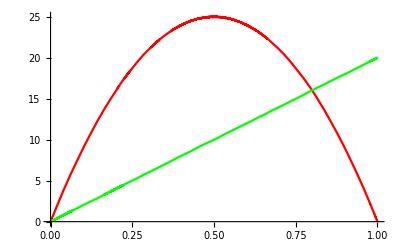

```mathematica
Plot[{f,g},{T,0,1},PlotStyle->{Red,Green}]
```

#### Trajectory for particle in electric field (t versus x) :

```mathematica
Simplify[Re[solx//.Test//.Solnn//.ϵ->0.5]]
```

3.14999+Re[(3.19784+0.0627174 ⅈ) ⅇ^((-7.08198+5.57341 ⅈ) T)-(0.0020721-0.00171076 ⅈ) ⅇ^((7.08198-5.57341 ⅈ) T)+ⅇ^((3.54099-2.7867 ⅈ) T) ((-0.0203674-0.154234 ⅈ)-(0.148279-0.22676 ⅈ) T)-(0.299986-0.469295 ⅈ) T+ⅇ^((-3.54099+2.7867 ⅈ) T) ((-6.32539+0.324453 ⅈ)+(7.51553-5.55825 ⅈ) T)]

```mathematica
Test ={xa->0,xb->5,ta->0,tb->0,m->1,k->1,C[1]->-1,H->1}
```

{xa→0,xb→5,ta→0,tb→0,m→1,k→1,C[1]→-1,H→1}

```mathematica
Solnn1
```

{n→3.57859-2.51206 ⅈ}

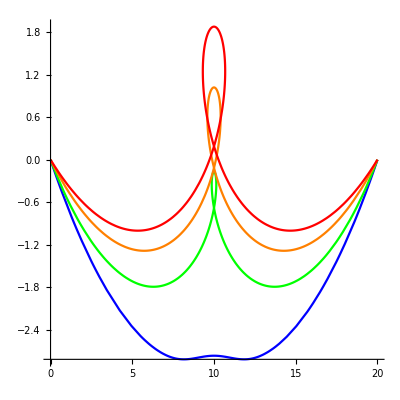

```mathematica
Show[ParametricPlot[{Re[solx/.Test/.Solnn//.ϵ->0.1],Im[solt/.Test/.Solnn//.ϵ->0.1]},{T,0,1},AspectRatio->1,PlotStyle->{Blue}],ParametricPlot[{Re[solx/.Test/.Solnn1//.ϵ->0.2],Im[solt/.Test/.Solnn1//.ϵ->0.2]},{T,0,1},AspectRatio->1,PlotStyle->{Green}],
ParametricPlot[{Re[solx/.Test/.Solnn2//.ϵ->0.3],Im[solt/.Test/.Solnn2//.ϵ->0.3]},{T,0,1},AspectRatio->1,PlotStyle->{Orange}],
ParametricPlot[{Re[solx/.Test/.Solnn3//.ϵ->0.4],Im[solt/.Test/.Solnn3//.ϵ->0.4]},{T,0,1},AspectRatio->1,PlotStyle->{Red}], PlotRange->All
]
```

```mathematica
Soln0
```

{{n→ConditionalExpression[(m (2 ⅈ π C[1]+Log[-(-2 m^2-k^2 ta^2+2 k^2 ta tb-k^2 tb^2+k^2 xa^2-2 k^2 xa xb+k^2 xb^2-√(-4 m^4+(2 m^2+k^2 ta^2-2 k^2 ta tb+k^2 tb^2-k^2 xa^2+2 k^2 xa xb-k^2 xb^2)^2))/(2 m^2)]))/k,C[1]∈ℤ]},{n→ConditionalExpression[(m (2 ⅈ π C[1]+Log[-(-2 m^2-k^2 ta^2+2 k^2 ta tb-k^2 tb^2+k^2 xa^2-2 k^2 xa xb+k^2 xb^2+√(-4 m^4+(2 m^2+k^2 ta^2-2 k^2 ta tb+k^2 tb^2-k^2 xa^2+2 k^2 xa xb-k^2 xb^2)^2))/(2 m^2)]))/k,C[1]∈ℤ]}}

```mathematica
Soln0[[1]]/.C[1]->-1//.ϵ->0//.Test//N
```

{n→9.16973+6.28319 ⅈ}

```mathematica
thickness=0.005;Show[ParametricPlot3D[{Re[solx/.Test/.Soln0[[2]]//.ϵ->0]//.Test,Im[solt/.Test/.Soln0[[2]]/.C[1]->-1//.ϵ->0]//.Test,Re[solt/.Test/.Soln0[[2]]/.C[1]->-1//.ϵ->0]//.Test},{T,0,1},AspectRatio->1,PlotStyle->{Black,Thickness[thickness]}],ParametricPlot3D[{Re[solx/.Test/.Solnn//.ϵ->0.1],Im[solt/.Test/.Solnn//.ϵ->0.1],Re[solt/.Test/.Solnn//.ϵ->0.1]},{T,0,1},AspectRatio->1,PlotStyle->{Blue,Thickness[thickness]}],ParametricPlot3D[{Re[solx/.Test/.Solnn1//.ϵ->0.2],Im[solt/.Test/.Solnn1//.ϵ->0.2],Re[solt/.Test/.Solnn1//.ϵ->0.2]},{T,0,1},AspectRatio->1,PlotStyle->{Green,Thickness[thickness]}],
ParametricPlot3D[{Re[solx/.Test/.Solnn2//.ϵ->0.3],Im[solt/.Test/.Solnn2//.ϵ->0.3],Re[solt/.Test/.Solnn2//.ϵ->0.3]},{T,0,1},AspectRatio->1,PlotStyle->{Orange,Thickness[thickness]}],
ParametricPlot3D[{Re[solx/.Test/.Solnn3//.ϵ->0.4],Im[solt/.Test/.Solnn3//.ϵ->0.4], Re[solt/.Test/.Solnn3//.ϵ->0.4]},{T,0,1},AspectRatio->1,PlotStyle->{Red,Thickness[thickness]}], PlotRange->All, AxesLabel->{"Re[x]","Im[t]","Re[t]"},ImageSize->600
]
```

-Graphics3D-

### Attempt at Manipulate function:

```mathematica
par2
```

{xa→0,ta→0,tb→0,n→1,k→0.5,H→0.1,ϵ→1}

```mathematica
FullSimplify[solt/.par2/.T->0.5]
```

1/((-1.+ⅇ^(0.5/m))^3 m)ⅇ^(-0.25/m) (ⅇ^(1./m) (-2. m-0.025 xb)+ⅇ^(0.25/m) m (-0.5-0.00625 xb)+ⅇ^(0.5/m) (m (1.-0.0125 xb)-0.00625 xb)+ⅇ^(1.5/m) (m (1.+0.0125 xb)-0.00625 xb)+ⅇ^(1.75/m) m (-0.5+0.00625 xb)+ⅇ^(1.25/m) (m (0.5-0.04375 xb)+0.01875 xb)+ⅇ^(0.75/m) (m (0.5+0.04375 xb)+0.01875 xb)) xb

```mathematica
FullSimplify[solx/.par2/.T->0.5]
```

0.5 xb

```mathematica
Manipulate[ 
ParametricPlot[{1/(16 (-1+ⅇ^((k n)/m))^3 m)ⅇ^(-(k n T)/m) (3 ⅇ^((3 k n T)/m) H m (ta-tb+xa-xb)^2 ϵ-3 ⅇ^((k n (1+3 T))/m) H m (ta-tb+xa-xb)^2 ϵ+3 ⅇ^(-(k n (-3+T))/m) H m (ta-tb-xa+xb)^2 ϵ-3 ⅇ^(-(k n (-2+T))/m) H m (ta-tb-xa+xb)^2 ϵ-2 ⅇ^((k n (3+T))/m) m (-4 ta+4 tb-4 (xa+xb)+H ta^2 ϵ-H tb^2 ϵ)-2 ⅇ^((k n T)/m) m (-4 ta+4 tb+4 (xa+xb)+H ta^2 ϵ-H tb^2 ϵ)-4 ⅇ^((2 k n)/m) (-H k n (ta-tb-xa+xb) ((-1+T) ta+T tb-xa+xb) ϵ+m (-4 ta+4 tb+4 xa-4 xb+H ta^2 ϵ-H tb^2 ϵ))-4 ⅇ^((k n (1+2 T))/m) (H k n (ta-tb+xa-xb) ((-1+T) ta+T tb+xa-xb) ϵ+m (-4 ta+4 tb-4 xa+4 xb+H ta^2 ϵ-H tb^2 ϵ))-ⅇ^((3 k n)/m) (2 H k n T (ta^2-(tb+xa-xb)^2) ϵ+m (H ta^2 ϵ+5 H tb^2 ϵ+(xa-xb) (-8+3 H (xa-xb) ϵ)+tb (-8+6 H (xa-xb) ϵ)+ta (8-6 H (tb+xa-xb) ϵ)))+ⅇ^((k n)/m) (-2 H k n (-1+T) (ta^2-tb^2-2 ta (xa-xb)+(xa-xb)^2) ϵ+m (5 H ta^2 ϵ+H tb^2 ϵ+(xa-xb) (8+3 H (xa-xb) ϵ)+tb (8+6 H (xa-xb) ϵ)-2 ta (4+3 H (tb+xa-xb) ϵ)))+2 ⅇ^((k n (2+T))/m) (-H k n ((-3+2 T) ta^2-2 ta ((-1+2 T) tb+xa-xb)+(tb+xa-xb) (tb+2 T tb+xa-2 T xa-xb+2 T xb)) ϵ+m (-12 (xa+xb)+H ta^2 ϵ-H tb^2 ϵ+tb (4+6 H (xa-xb) ϵ)+ta (-4+6 H (-xa+xb) ϵ)))+2 ⅇ^((k n (1+T))/m) (H k n ((-3+2 T) ta^2+(tb+2 T tb+(-1+2 T) (xa-xb)) (tb-xa+xb)-2 ta ((-1+2 T) tb-xa+xb)) ϵ+m (12 (xa+xb)+H ta^2 ϵ-H tb^2 ϵ+ta (-4+6 H (xa-xb) ϵ)+tb (4+6 H (-xa+xb) ϵ)))-ⅇ^((2 k n T)/m) (2 H k n T (-ta^2+(tb-xa+xb)^2) ϵ+m (H ta^2 ϵ+5 H tb^2 ϵ+(xa-xb) (8+3 H (xa-xb) ϵ)+tb (-8+6 H (-xa+xb) ϵ)+ta (8-6 H (tb-xa+xb) ϵ)))+ⅇ^((2 k n (1+T))/m) (2 H k n (-1+T) (ta^2-tb^2+2 ta (xa-xb)+(xa-xb)^2) ϵ+m (5 H ta^2 ϵ+H tb^2 ϵ+(xa-xb) (-8+3 H (xa-xb) ϵ)+tb (8+6 H (-xa+xb) ϵ)-2 ta (4+3 H (tb-xa+xb) ϵ)))),1/(16 (-1+ⅇ^((k n)/m))^3 m)ⅇ^(-(k n T)/m) (2 ⅇ^((3 k n T)/m) H m (ta-tb+xa-xb)^2 ϵ-2 ⅇ^((k n (1+3 T))/m) H m (ta-tb+xa-xb)^2 ϵ-2 ⅇ^(-(k n (-3+T))/m) H m (ta-tb-xa+xb)^2 ϵ+2 ⅇ^(-(k n (-2+T))/m) H m (ta-tb-xa+xb)^2 ϵ-ⅇ^((k n (3+T))/m) m (H ta^2 ϵ+H tb^2 ϵ-2 tb (4+H (xa-xb) ϵ)-(xa-xb) (8+H (xa-xb) ϵ)-2 ta (4+H (tb+xa-xb) ϵ))+ⅇ^((k n T)/m) m (H ta^2 ϵ+H tb^2 ϵ-(xa-xb) (-8+H (xa-xb) ϵ)+2 tb (-4+H (xa-xb) ϵ)-2 ta (4+H (tb-xa+xb) ϵ))+4 ⅇ^((k n (1+2 T))/m) (-H k n (ta-tb+xa-xb) ((-1+T) ta+T tb+xa-xb) ϵ+m (4 (xa-xb)+tb (-4+H (xa-xb) ϵ)+ta (4+H (xa-xb) ϵ)))+4 ⅇ^((2 k n)/m) (-H k n (ta-tb-xa+xb) ((-1+T) ta+T tb-xa+xb) ϵ+m (4 (xa-xb)+ta (-4+H (xa-xb) ϵ)+tb (4+H (xa-xb) ϵ)))+ⅇ^((3 k n)/m) (2 H k n T (ta^2-(tb+xa-xb)^2) ϵ+m (3 H ta^2 ϵ+3 H tb^2 ϵ+(xa-xb) (-8+H (xa-xb) ϵ)+2 tb (-4+H (xa-xb) ϵ)+ta (8-6 H (tb+xa-xb) ϵ)))+ⅇ^((k n)/m) (2 H k n (-1+T) (ta^2-tb^2-2 ta (xa-xb)+(xa-xb)^2) ϵ-m (3 H ta^2 ϵ+3 H tb^2 ϵ+(xa-xb) (8+H (xa-xb) ϵ)+tb (8+6 H (xa-xb) ϵ)-2 ta (4+H (3 tb+xa-xb) ϵ)))+ⅇ^((k n (1+T))/m) (-2 H k n (ta^2+tb^2+2 tb (xa-xb)-3 (xa-xb)^2-2 ta (tb-xa+xb)) ϵ+m (5 H ta^2 ϵ+5 H tb^2 ϵ+(xa-xb) (-8+3 H (xa-xb) ϵ)-2 ta (-12+H (5 tb+xa-xb) ϵ)+tb (24+2 H (-xa+xb) ϵ)))-ⅇ^((2 k n T)/m) (2 H k n T (-ta^2+(tb-xa+xb)^2) ϵ+m (3 H ta^2 ϵ+3 H tb^2 ϵ-2 tb (4+H (xa-xb) ϵ)+(xa-xb) (8+H (xa-xb) ϵ)+ta (8-6 H (tb-xa+xb) ϵ)))+ⅇ^((2 k n (1+T))/m) (2 H k n (-1+T) (ta^2-tb^2+2 ta (xa-xb)+(xa-xb)^2) ϵ+m (3 H ta^2 ϵ+3 H tb^2 ϵ+(xa-xb) (-8+H (xa-xb) ϵ)+tb (8+6 H (-xa+xb) ϵ)-2 ta (4+H (3 tb-xa+xb) ϵ)))-ⅇ^((k n (2+T))/m) (2 H k n (ta^2+tb^2-2 tb (xa-xb)-3 (xa-xb)^2-2 ta (tb+xa-xb)) ϵ+m (5 H ta^2 ϵ+5 H tb^2 ϵ+2 tb (12+H (xa-xb) ϵ)+(xa-xb) (8+3 H (xa-xb) ϵ)-2 ta (-12+H (5 tb-xa+xb) ϵ))))},{T,0,1},AspectRatio->1,ImageSize->500,PlotRange->All, AxesLabel->{x,t}]
,
{{xa,0},-25,25},
{{xb,2},-25,25},
{{ta,0},0,10},
{{tb,0},0,10},
{{m,0.001},0.0001,100},
{{k,0.5},-1,5},
{{n,1},0,10},
{{H,0.1},0,1},
{{ϵ,1},0,1}]
```

```mathematica
parameters={xa->0,xb->20,ta-> 0, tb -> 0,m->4,n->6, k->3};
parameters1={xa->0,xb->20,ta-> 0, tb -> 0,m->0.0001,n->6, k->3};
parameters2={xa->0,xb->20,ta-> 0, tb -> 20,m->4,n->6, k->3};
parameters3={xa->0,xb->20,ta-> 0, tb -> 40,m->4,n->1.5, k->3};
parameters4={xa->0,xb->20,ta-> 0, tb -> 40,m->4,n->6, k->3};
```

```mathematica
solx/.parameters
```

20 Cosh[9/4 (-1+T)] Csch[9/4] Sinh[(9 T)/4]

## Find the classical action:

```mathematica
L1=Series[L/.pert,{ϵ,0,1}]//FullSimplify//Normal
```

k x0[T] t0'[T]-(m (n^2+t0'[T]^2-x0'[T]^2))/(2 n)+(ϵ (2 k n x1[T] t0'[T]+2 k n x0[T] t1'[T]-2 m t0'[T] t1'[T]+H m t0[T] x0'[T]^2+2 m x0'[T] x1'[T]))/(2 n)

```mathematica
LL =L1//.pert3//.pert5(*//.{tb->1,ta->1}*) (* Storing the Lagrangian with the solution plugged in *)
```

-(ⅇ^(-(k n T)/m) k (ⅇ^(1/m) ta-ⅇ^1 ta+21) ((ⅇ^(-(k n T)/m) k n (-ⅇ^((k n)/m) ta+ⅇ^(1/m) ta+20+ⅇ^(1/m) xb))/(2 (-1+ⅇ^((k n)/m)) m)-(ⅇ^(-1/m) (1/m+16+1/m))/(2 (-1+ⅇ^(1/m)))))/(2 (-1+ⅇ^((k n)/m)))-(m (n^2-(1)^2+(1-1)^2))/(2 n)+(((ⅇ^(-1/m) H k n (1) (1))/(16 (-1+1)^4 m)+4+(H 11(1))/(8 1^3)) ϵ)/(2 n)
 |  |  |  |

```mathematica
SclIndef=Integrate[LL,T](* Integrating the Lagrangian over T to get the classical action *)
```

-(n T (m^2-2 ⅇ^((k n)/m) m^2+ⅇ^((2 k n)/m) m^2+ⅇ^((k n)/m) k^2 ta^2-2 ⅇ^((k n)/m) k^2 ta tb+ⅇ^((k n)/m) k^2 tb^2-ⅇ^((k n)/m) k^2 xa^2+2 ⅇ^((k n)/m) k^2 xa xb-ⅇ^((k n)/m) k^2 xb^2))/(2 (-1+ⅇ^((k n)/m))^2 m)-(ⅇ^((3 k n T)/m) m (1)^2 ((ⅇ^(-1/m) k n (1))/(2 (-1+ⅇ^(1/m)) m)-(ⅇ^1 1)/(2 (1))))/(4 (-1+ⅇ^1) n (ⅇ^((k n)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m) tb-ⅇ^(1/m) tb-ⅇ^1 xa+ⅇ^(1/m) xa+ⅇ^((k n)/m) xb-ⅇ^((2 k n T)/m) xb))+10+(ⅇ^1 11ϵ)/(2 n)+(ⅇ^(-(k n T)/m) ((ⅇ^((k n)/m) H k n (1))/(16 (-1+ⅇ^1)^4 m)-(T (1))/(8 (1)^3 k m n)) ϵ)/(2 n)
 |  |  |  |

```mathematica
Scl=Simplify[(SclIndef/.T->1)-(SclIndef/.T->0)]
```

1/48 (-24 m n-(6 ⅇ^((k n)/m) H k^2 n ((-1+ⅇ^((k n)/m)) ta+(-1+ⅇ^((k n)/m)) tb+(1+ⅇ^((k n)/m)) (xa-xb)) (ta^2-2 ta tb+tb^2-(xa-xb)^2) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+1/((-1+ⅇ^((k n)/m))^2)k (3 (-1+ⅇ^((2 k n)/m)) H ta^3 ϵ+3 (-1+ⅇ^((2 k n)/m)) H tb^3 ϵ-3 tb^2 (-4+H (xa-xb) ϵ-6 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (4+H (xa-xb) ϵ))+(xa-xb)^2 (-12+H (xa-xb) ϵ-14 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (12+H (xa-xb) ϵ))-3 ta^2 (-4-6 ⅇ^((k n)/m) H (xa-xb) ϵ-H (tb-xa+xb) ϵ+ⅇ^((2 k n)/m) (4+H (tb+xa-xb) ϵ))+3 (-1+ⅇ^((k n)/m)) tb ((1+ⅇ^((k n)/m)) H xa^2 ϵ-2 xa (4+H xb ϵ+ⅇ^((k n)/m) (-4+H xb ϵ))+xb (-8+H xb ϵ+ⅇ^((k n)/m) (8+H xb ϵ)))+3 ta (-(-1+ⅇ^((2 k n)/m)) H tb^2 ϵ+2 tb (-4+H (xa-xb) ϵ-6 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (4+H (xa-xb) ϵ))+(-1+ⅇ^((k n)/m)) ((1+ⅇ^((k n)/m)) H xa^2 ϵ+xb (8+H xb ϵ+ⅇ^((k n)/m) (-8+H xb ϵ))-2 xa (-4+H xb ϵ+ⅇ^((k n)/m) (4+H xb ϵ))))))

```mathematica
(Scl)/.ϵ->0//FullSimplify
```

```mathematica
D[Coth[x],x]
```

-Csch[x]^2

```mathematica
1/4 (-2 (m n+k (ta-tb) (xa+xb))-k (ta-tb+xa-xb) (ta-tb-xa+xb))
```

```mathematica
D[Scl,n]//ExpToTrig//Simplify
```

-1/(64 m^2)Csch[(k n)/(2 m)]^4 (12 m^3+4 k^2 m ta^2-8 k^2 m ta tb+4 k^2 m tb^2-4 k^2 m xa^2+8 k^2 m xa xb-4 k^2 m xb^2-2 H k^2 m ta^3 ϵ+2 H k^2 m ta^2 tb ϵ+2 H k^2 m ta tb^2 ϵ-2 H k^2 m tb^3 ϵ-2 H k^3 n ta^2 xa ϵ+4 H k^3 n ta tb xa ϵ-2 H k^3 n tb^2 xa ϵ+2 H k^3 n xa^3 ϵ+2 H k^3 n ta^2 xb ϵ-4 H k^3 n ta tb xb ϵ+2 H k^3 n tb^2 xb ϵ-6 H k^3 n xa^2 xb ϵ+6 H k^3 n xa xb^2 ϵ-2 H k^3 n xb^3 ϵ+(-16 m^3+H k^3 n (-ta^2+2 ta tb-tb^2+(xa-xb)^2) (xa-xb) ϵ+2 k^2 m (-2 tb^2+2 (xa-xb)^2+H ta^3 ϵ+H tb^3 ϵ+ta tb (4-H tb ϵ)-ta^2 (2+H tb ϵ))) Cosh[(k n)/m]+4 m^3 Cosh[(2 k n)/m]-H k^3 n ta^3 ϵ Sinh[(k n)/m]+H k^3 n ta^2 tb ϵ Sinh[(k n)/m]+H k^3 n ta tb^2 ϵ Sinh[(k n)/m]-H k^3 n tb^3 ϵ Sinh[(k n)/m]+3 H k^2 m ta^2 xa ϵ Sinh[(k n)/m]-6 H k^2 m ta tb xa ϵ Sinh[(k n)/m]+3 H k^2 m tb^2 xa ϵ Sinh[(k n)/m]+H k^3 n ta xa^2 ϵ Sinh[(k n)/m]+H k^3 n tb xa^2 ϵ Sinh[(k n)/m]-3 H k^2 m xa^3 ϵ Sinh[(k n)/m]-3 H k^2 m ta^2 xb ϵ Sinh[(k n)/m]+6 H k^2 m ta tb xb ϵ Sinh[(k n)/m]-3 H k^2 m tb^2 xb ϵ Sinh[(k n)/m]-2 H k^3 n ta xa xb ϵ Sinh[(k n)/m]-2 H k^3 n tb xa xb ϵ Sinh[(k n)/m]+9 H k^2 m xa^2 xb ϵ Sinh[(k n)/m]+H k^3 n ta xb^2 ϵ Sinh[(k n)/m]+H k^3 n tb xb^2 ϵ Sinh[(k n)/m]-9 H k^2 m xa xb^2 ϵ Sinh[(k n)/m]+3 H k^2 m xb^3 ϵ Sinh[(k n)/m])

```mathematica
ComplexExpand[Re[3y+ⅈ x]]
```

3 y

```mathematica
D[FullSimplify[(Scl),n]]//Simplify (* Using simplified initial values for x and t *)
```

$Aborted

## Evaluate the prefactor

This is not its derivation but just an evaluation where the prefactor is 1/Sqrt(Det[mx]) where the mx is a matrix with entries given below by Scl1, Scl2, Scl3, and Scl4.

```mathematica
Scl1=D[Scl,xa,xb] (* Evaluating each entry in the matrix *)
```

1/48 (-(12 ⅇ^((k n)/m) H k^2 n ((-1+ⅇ^((k n)/m)) ta+(-1+ⅇ^((k n)/m)) tb+(1+ⅇ^((k n)/m)) (xa-xb)) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+(12 ⅇ^((k n)/m) (-1-ⅇ^((k n)/m)) H k^2 n (xa-xb) ϵ)/((-1+ⅇ^((k n)/m))^3 m)-(12 ⅇ^((k n)/m) (1+ⅇ^((k n)/m)) H k^2 n (xa-xb) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+1/((-1+ⅇ^((k n)/m))^2)k (-6 (-1+ⅇ^((k n)/m)) ta (H ϵ+ⅇ^((k n)/m) H ϵ)-6 (-1+ⅇ^((k n)/m)) tb (H ϵ+ⅇ^((k n)/m) H ϵ)+2 (xa-xb) (-H ϵ+14 ⅇ^((k n)/m) H ϵ-ⅇ^((2 k n)/m) H ϵ)-2 (xa-xb) (H ϵ-14 ⅇ^((k n)/m) H ϵ+ⅇ^((2 k n)/m) H ϵ)-2 (-12+H (xa-xb) ϵ-14 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (12+H (xa-xb) ϵ))))

```mathematica
Scl2 = D[Scl,xa,tb]
```

1/48 (-(6 ⅇ^((k n)/m) (1+ⅇ^((k n)/m)) H k^2 n (-2 ta+2 tb) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+(12 ⅇ^((k n)/m) H k^2 n (xa-xb) ϵ)/((-1+ⅇ^((k n)/m))^2 m)+(k (6 ta (H ϵ-6 ⅇ^((k n)/m) H ϵ+ⅇ^((2 k n)/m) H ϵ)-6 tb (H ϵ-6 ⅇ^((k n)/m) H ϵ+ⅇ^((2 k n)/m) H ϵ)+3 (-1+ⅇ^((k n)/m)) (2 (1+ⅇ^((k n)/m)) H xa ϵ-2 (4+H xb ϵ+ⅇ^((k n)/m) (-4+H xb ϵ)))))/((-1+ⅇ^((k n)/m))^2))

```mathematica
Scl3 = D[Scl,ta,xb]
```

1/48 (-(6 ⅇ^((k n)/m) (-1-ⅇ^((k n)/m)) H k^2 n (2 ta-2 tb) ϵ)/((-1+ⅇ^((k n)/m))^3 m)-(12 ⅇ^((k n)/m) H k^2 n (xa-xb) ϵ)/((-1+ⅇ^((k n)/m))^2 m)+(k (-6 ta (-H ϵ+6 ⅇ^((k n)/m) H ϵ-ⅇ^((2 k n)/m) H ϵ)+3 (2 tb (-H ϵ+6 ⅇ^((k n)/m) H ϵ-ⅇ^((2 k n)/m) H ϵ)+(-1+ⅇ^((k n)/m)) (8+H xb ϵ-2 xa (H ϵ+ⅇ^((k n)/m) H ϵ)+xb (H ϵ+ⅇ^((k n)/m) H ϵ)+ⅇ^((k n)/m) (-8+H xb ϵ)))))/((-1+ⅇ^((k n)/m))^2))

```mathematica
Scl4 = D[Scl,ta,tb]
```

1/48 (-(6 ⅇ^((k n)/m) H k^2 n (2 ta-2 tb) ϵ)/((-1+ⅇ^((k n)/m))^2 m)-(6 ⅇ^((k n)/m) H k^2 n (-2 ta+2 tb) ϵ)/((-1+ⅇ^((k n)/m))^2 m)+(12 ⅇ^((k n)/m) H k^2 n ((-1+ⅇ^((k n)/m)) ta+(-1+ⅇ^((k n)/m)) tb+(1+ⅇ^((k n)/m)) (xa-xb)) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+(k (-6 ta (-H ϵ+ⅇ^((2 k n)/m) H ϵ)+3 (-2 (-1+ⅇ^((2 k n)/m)) H tb ϵ+2 (-4+H (xa-xb) ϵ-6 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (4+H (xa-xb) ϵ)))))/((-1+ⅇ^((k n)/m))^2))

```mathematica
Mx=({{Scl1, Scl2}, {Scl3, Scl4}}) (* Plugging in all the evaluated entries *)
```

{{1/48 (-(12 ⅇ^((k n)/m) H k^2 n ((-1+ⅇ^((k n)/m)) ta+(-1+ⅇ^((k n)/m)) tb+(1+ⅇ^((k n)/m)) (xa-xb)) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+(12 ⅇ^((k n)/m) (-1-ⅇ^((k n)/m)) H k^2 n (xa-xb) ϵ)/((-1+ⅇ^((k n)/m))^3 m)-(12 ⅇ^((k n)/m) (1+ⅇ^((k n)/m)) H k^2 n (xa-xb) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+1/((-1+ⅇ^((k n)/m))^2)k (-6 (-1+ⅇ^((k n)/m)) ta (H ϵ+ⅇ^((k n)/m) H ϵ)-6 (-1+ⅇ^((k n)/m)) tb (H ϵ+ⅇ^((k n)/m) H ϵ)+2 (xa-xb) (-H ϵ+14 ⅇ^((k n)/m) H ϵ-ⅇ^((2 k n)/m) H ϵ)-2 (xa-xb) (H ϵ-14 ⅇ^((k n)/m) H ϵ+ⅇ^((2 k n)/m) H ϵ)-2 (-12+H (xa-xb) ϵ-14 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (12+H (xa-xb) ϵ)))),1/48 (-(6 ⅇ^((k n)/m) (1+ⅇ^((k n)/m)) H k^2 n (-2 ta+2 tb) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+(12 ⅇ^((k n)/m) H k^2 n (xa-xb) ϵ)/((-1+ⅇ^((k n)/m))^2 m)+(k (6 ta (H ϵ-6 ⅇ^((k n)/m) H ϵ+ⅇ^((2 k n)/m) H ϵ)-6 tb (H ϵ-6 ⅇ^((k n)/m) H ϵ+ⅇ^((2 k n)/m) H ϵ)+3 (-1+ⅇ^((k n)/m)) (2 (1+ⅇ^((k n)/m)) H xa ϵ-2 (4+H xb ϵ+ⅇ^((k n)/m) (-4+H xb ϵ)))))/((-1+ⅇ^((k n)/m))^2))},{1/48 (-(6 ⅇ^((k n)/m) (-1-ⅇ^((k n)/m)) H k^2 n (2 ta-2 tb) ϵ)/((-1+ⅇ^((k n)/m))^3 m)-(12 ⅇ^((k n)/m) H k^2 n (xa-xb) ϵ)/((-1+ⅇ^((k n)/m))^2 m)+(k (-6 ta (-H ϵ+6 ⅇ^((k n)/m) H ϵ-ⅇ^((2 k n)/m) H ϵ)+3 (2 tb (-H ϵ+6 ⅇ^((k n)/m) H ϵ-ⅇ^((2 k n)/m) H ϵ)+(-1+ⅇ^((k n)/m)) (8+H xb ϵ-2 xa (H ϵ+ⅇ^((k n)/m) H ϵ)+xb (H ϵ+ⅇ^((k n)/m) H ϵ)+ⅇ^((k n)/m) (-8+H xb ϵ)))))/((-1+ⅇ^((k n)/m))^2)),1/48 (-(6 ⅇ^((k n)/m) H k^2 n (2 ta-2 tb) ϵ)/((-1+ⅇ^((k n)/m))^2 m)-(6 ⅇ^((k n)/m) H k^2 n (-2 ta+2 tb) ϵ)/((-1+ⅇ^((k n)/m))^2 m)+(12 ⅇ^((k n)/m) H k^2 n ((-1+ⅇ^((k n)/m)) ta+(-1+ⅇ^((k n)/m)) tb+(1+ⅇ^((k n)/m)) (xa-xb)) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+(k (-6 ta (-H ϵ+ⅇ^((2 k n)/m) H ϵ)+3 (-2 (-1+ⅇ^((2 k n)/m)) H tb ϵ+2 (-4+H (xa-xb) ϵ-6 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (4+H (xa-xb) ϵ)))))/((-1+ⅇ^((k n)/m))^2))}}

```mathematica
Pref=Simplify[1/(√Det[Mx])] (* Evaluating and simplifying the full prefactor *)
```

4/(√(1/((-1+ⅇ^((k n)/m))^6 m^2)k^2 (H^2 m^2 ta tb ϵ^2+ⅇ^((6 k n)/m) H^2 m^2 ta tb ϵ^2+2 ⅇ^((3 k n)/m) (4 H^2 k^2 n^2 (ta tb-(xa-xb)^2) ϵ^2-4 H k m n (xa-xb) ϵ (-5+3 H (ta+tb) ϵ)+m^2 (-48+H^2 (13 ta^2-24 ta tb+13 tb^2+27 (xa-xb)^2) ϵ^2))+ⅇ^((k n)/m) m (m (-16-16 H (xa-xb) ϵ+H^2 (3 ta^2+3 tb^2+2 tb (xa-xb)+5 (xa-xb)^2-2 ta (4 tb-xa+xb)) ϵ^2)+H k n ϵ (4 tb+H ta^2 ϵ+H tb^2 ϵ+ta (4-2 H tb ϵ)+(xa-xb) (-4+H (xa-xb) ϵ)))+ⅇ^((5 k n)/m) m (m (-16+16 H (xa-xb) ϵ+H^2 (3 ta^2+3 tb^2-2 tb (xa-xb)+5 (xa-xb)^2-2 ta (4 tb+xa-xb)) ϵ^2)-H k n ϵ (4 tb+H ta^2 ϵ+H tb^2 ϵ+ta (4-2 H tb ϵ)+(xa-xb) (4+H (xa-xb) ϵ)))-ⅇ^((2 k n)/m) (2 H^2 k^2 n^2 (ta^2-2 ta (xa-xb)+(tb-xa+xb)^2) ϵ^2+m^2 (-64-32 H (xa-xb) ϵ+H^2 (16 ta^2+4 (4 tb^2+tb (xa-xb)+8 (xa-xb)^2)+ta (-31 tb+4 xa-4 xb)) ϵ^2)+2 H k m n ϵ (3 H ta^2 ϵ+3 H tb^2 ϵ+(xa-xb) (8+7 H (xa-xb) ϵ)+ta (4-6 H (tb+xa-xb) ϵ)+tb (4+6 H (-xa+xb) ϵ)))+ⅇ^((4 k n)/m) (-2 H^2 k^2 n^2 (ta^2+2 ta (xa-xb)+(tb+xa-xb)^2) ϵ^2+m^2 (64-32 H (xa-xb) ϵ-H^2 (16 ta^2+ta (-31 tb-4 xa+4 xb)+4 (4 tb^2+8 (xa-xb)^2+tb (-xa+xb))) ϵ^2)+2 H k m n ϵ (3 H ta^2 ϵ+3 H tb^2 ϵ+tb (4+6 H (xa-xb) ϵ)+(xa-xb) (-8+7 H (xa-xb) ϵ)+ta (4-6 H (tb-xa+xb) ϵ))))))

## Figure out how to find the kernel!

The kernel is ultimately an integral over N from 0 to ∞ of the integrand below (stored as Int):

```mathematica
Int = Simplify[Pref*Exp[ⅈ Scl/ℏ]]
```

(4 ⅇ^((ⅈ (-24 m n-(6 ⅇ^((k n)/m) H k^2 n ((-1+ⅇ^((k n)/m)) ta+(-1+ⅇ^((k n)/m)) tb+(1+ⅇ^((k n)/m)) (xa-xb)) (ta^2-2 ta tb+tb^2-(xa-xb)^2) ϵ)/((-1+ⅇ^((k n)/m))^3 m)+(k (3 (-1+ⅇ^((2 k n)/m)) H ta^3 ϵ+3 (-1+ⅇ^((2 k n)/m)) H tb^3 ϵ-3 tb^2 (-4+H (xa-xb) ϵ-6 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (4+H (xa-xb) ϵ))+(xa-xb)^2 (-12+H (xa-xb) ϵ-14 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (12+H (xa-xb) ϵ))-3 ta^2 (-4-6 ⅇ^((k n)/m) H (xa-xb) ϵ-H (tb-xa+xb) ϵ+ⅇ^((2 k n)/m) (4+H (tb+xa-xb) ϵ))+3 (-1+ⅇ^((k n)/m)) tb ((1+ⅇ^((k n)/m)) H xa^2 ϵ-2 xa (4+H xb ϵ+ⅇ^((k n)/m) (-4+H xb ϵ))+xb (-8+H xb ϵ+ⅇ^((k n)/m) (8+H xb ϵ)))+3 ta (-(-1+ⅇ^((2 k n)/m)) H tb^2 ϵ+2 tb (-4+H (xa-xb) ϵ-6 ⅇ^((k n)/m) H (xa-xb) ϵ+ⅇ^((2 k n)/m) (4+H (xa-xb) ϵ))+(-1+ⅇ^((k n)/m)) ((1+ⅇ^((k n)/m)) H xa^2 ϵ+xb (8+H xb ϵ+ⅇ^((k n)/m) (-8+H xb ϵ))-2 xa (-4+H xb ϵ+ⅇ^((k n)/m) (4+H xb ϵ))))))/((-1+ⅇ^((k n)/m))^2)))/(48 ℏ)))/(√(1/((-1+ⅇ^((k n)/m))^6 m^2)k^2 (H^2 m^2 ta tb ϵ^2+ⅇ^((6 k n)/m) H^2 m^2 ta tb ϵ^2+2 ⅇ^((3 k n)/m) (4 H^2 k^2 n^2 (ta tb-(xa-xb)^2) ϵ^2-4 H k m n (xa-xb) ϵ (-5+3 H (ta+tb) ϵ)+m^2 (-48+H^2 (13 ta^2-24 ta tb+13 tb^2+27 (xa-xb)^2) ϵ^2))+ⅇ^((k n)/m) m (m (-16-16 H (xa-xb) ϵ+H^2 (3 ta^2+3 tb^2+2 tb (xa-xb)+5 (xa-xb)^2-2 ta (4 tb-xa+xb)) ϵ^2)+H k n ϵ (4 tb+H ta^2 ϵ+H tb^2 ϵ+ta (4-2 H tb ϵ)+(xa-xb) (-4+H (xa-xb) ϵ)))+ⅇ^((5 k n)/m) m (m (-16+16 H (xa-xb) ϵ+H^2 (3 ta^2+3 tb^2-2 tb (xa-xb)+5 (xa-xb)^2-2 ta (4 tb+xa-xb)) ϵ^2)-H k n ϵ (4 tb+H ta^2 ϵ+H tb^2 ϵ+ta (4-2 H tb ϵ)+(xa-xb) (4+H (xa-xb) ϵ)))-ⅇ^((2 k n)/m) (2 H^2 k^2 n^2 (ta^2-2 ta (xa-xb)+(tb-xa+xb)^2) ϵ^2+m^2 (-64-32 H (xa-xb) ϵ+H^2 (16 ta^2+4 (4 tb^2+tb (xa-xb)+8 (xa-xb)^2)+ta (-31 tb+4 xa-4 xb)) ϵ^2)+2 H k m n ϵ (3 H ta^2 ϵ+3 H tb^2 ϵ+(xa-xb) (8+7 H (xa-xb) ϵ)+ta (4-6 H (tb+xa-xb) ϵ)+tb (4+6 H (-xa+xb) ϵ)))+ⅇ^((4 k n)/m) (-2 H^2 k^2 n^2 (ta^2+2 ta (xa-xb)+(tb+xa-xb)^2) ϵ^2+m^2 (64-32 H (xa-xb) ϵ-H^2 (16 ta^2+ta (-31 tb-4 xa+4 xb)+4 (4 tb^2+8 (xa-xb)^2+tb (-xa+xb))) ϵ^2)+2 H k m n ϵ (3 H ta^2 ϵ+3 H tb^2 ϵ+tb (4+6 H (xa-xb) ϵ)+(xa-xb) (-8+7 H (xa-xb) ϵ)+ta (4-6 H (tb-xa+xb) ϵ))))))

However, this integral is extremely difficult (or impossible?) to solve analytically, so we need to use an approximation.

Specifically, we will use a saddle point approximation. That involves allowing N to be complex, and thus allowing the function (i.e. the integrand) to have dependence on complex N (introducing the complex plane). The original contour of the function in the complex plane is very much oscillatory, with an every increasing amplitude of oscillations, which is why it is so tough to solve the integral analytically.Using Cauchy’s theorem, we can deform the original oscillatory contour of the function, which would be a line integral in the 3D-space and restricted to real values of N, to any other “well-behaved” contour such that the contour does not pass over any undefined points (i.e. the function needs to be holomorphic), and the integral over this new contour would be the same as the original contour integral. To quote Wikipedia:  “...if two different paths connect the same two points, and a function is holomorphic everywhere in between the two paths, then the two path integrals of the function will be the same.” (More about holomorphic functions later?) 

Deforming the original path is helpful in the approximation process since the path can be deformed to pass through the highest stationary point/s, with other conditions satisfied of course, and then the path integral would be dominated by that stationary point (or points). It turns out that the only extrema possible in our case are saddle points, so we deform the path to pass through a saddle point (with steepest descent?). [https://www2.ph.ed.ac.uk/~dmarendu/MOMP/lecture05.pdf]

We have been talking about our oscillatory “function” as the whole integrand, but, ignoring the prefactor for now, truly what is relevant is the classical action, Scl, because when we set (d(Int))/dN=0 in order to find the extrema, we get (d(ⅈScl/ℏ))/dN e^(ⅈScl/ℏ)=0 , where the exponent term can’t go to 0, and ⅈ and ℏ are constants, so we know that the extrema are given by (d(Scl))/dN=0, thus the oscillatory function we are concerned with is just Scl.

### Saddle-point approximation

```mathematica
(* Re[fullinteg/.{xa->0,xb->1,ta->0,tb->1,m->1,k->1,ℏ->1}]//FullSimplify *)
```

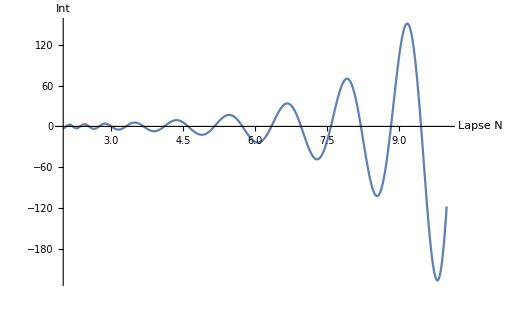

```mathematica
Plot[Re[Int/.{xa->0,xb->5,ta->0,tb->0,m->1,k->1,ℏ->0.1,ϵ->0.1,H->1}],{n,2,10},PlotRange->All,AxesLabel->{  HoldForm[N](Lapse), HoldForm[Int]},LabelStyle->{12, GrayLevel[0]}] (* Plot of the function showing oscillatory behavior *)
```

#### Find the saddle points:

```mathematica
Simplify[D[Scl, n]]
```

1/(8 m^2)(-4 m^3+(ⅇ^((k n)/m) H k^3 n ((-1+ⅇ^((2 k n)/m)) ta+(-1+ⅇ^((2 k n)/m)) tb+(1+4 ⅇ^((k n)/m)+ⅇ^((2 k n)/m)) (xa-xb)) (ta^2-2 ta tb+tb^2-(xa-xb)^2) ϵ)/((-1+ⅇ^((k n)/m))^4)-1/((-1+ⅇ^((k n)/m))^3)ⅇ^((k n)/m) k^2 m (2 (-1+ⅇ^((k n)/m)) H ta^3 ϵ+2 (-1+ⅇ^((k n)/m)) H tb^3 ϵ-2 ta tb (4-H (tb-3 xa+3 xb) ϵ+ⅇ^((k n)/m) (-4+H (tb+3 xa-3 xb) ϵ))+tb^2 (4+3 H (xa-xb) ϵ+ⅇ^((k n)/m) (-4+3 H (xa-xb) ϵ))-(xa-xb)^2 (4+3 H (xa-xb) ϵ+ⅇ^((k n)/m) (-4+3 H (xa-xb) ϵ))+ta^2 (4+H (2 tb+3 xa-3 xb) ϵ-ⅇ^((k n)/m) (4+H (2 tb-3 xa+3 xb) ϵ))))

```mathematica
Simplify[D[Scl, n]]/.ϵ->0;
```

```mathematica
Soln0=Solve[(ExpToTrig[%514]/.ϵ->0)==0,n]
```

{{n→ConditionalExpression[(m (2 ⅈ π C[1]+Log[-(-2 m^2-k^2 ta^2+2 k^2 ta tb-k^2 tb^2+k^2 xa^2-2 k^2 xa xb+k^2 xb^2-√(-4 m^4+(2 m^2+k^2 ta^2-2 k^2 ta tb+k^2 tb^2-k^2 xa^2+2 k^2 xa xb-k^2 xb^2)^2))/(2 m^2)]))/k,C[1]∈ℤ]},{n→ConditionalExpression[(m (2 ⅈ π C[1]+Log[-(-2 m^2-k^2 ta^2+2 k^2 ta tb-k^2 tb^2+k^2 xa^2-2 k^2 xa xb+k^2 xb^2+√(-4 m^4+(2 m^2+k^2 ta^2-2 k^2 ta tb+k^2 tb^2-k^2 xa^2+2 k^2 xa xb-k^2 xb^2)^2))/(2 m^2)]))/k,C[1]∈ℤ]}}

```mathematica
FullSimplify[n/.Soln0[[1]]/.C[1]->2]
```

(m (4 ⅈ π+Log[(2 m^2+k^2 (ta-tb+xa-xb) (ta-tb-xa+xb)+√(-4 m^4+(2 m^2+k^2 (ta-tb+xa-xb) (ta-tb-xa+xb))^2))/(2 m^2)]))/k

```mathematica
FullSimplify[n/.Soln0[[2]]/.C[1]->2]
```

(m (4 ⅈ π+Log[(2 m^2+k^2 (ta-tb+xa-xb) (ta-tb-xa+xb)-√(-4 m^4+(2 m^2+k^2 (ta-tb+xa-xb) (ta-tb-xa+xb))^2))/(2 m^2)]))/k

```mathematica
FullSimplify[TrigToExp[(2 m (-ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k/.C[1]->1]];
```

```mathematica
FullSimplify[TrigToExp[(2 m (ⅈ π-ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k/.C[1]->1]];
```

```mathematica
Series[Simplify[(SeriesCoefficient[Simplify[D[Scl, n]],{ϵ,0,1}])],{H,0,2}];
```

```mathematica
Simplify[SeriesCoefficient[Series[Simplify[D[Scl, n]],{ϵ,0,1}],1]];
```

```mathematica
Soln1=FindRoot[(Simplify[SeriesCoefficient[Series[Simplify[D[Scl, n]],{ϵ,0,1}],1]]//.Test)==0, {n,0.5+0.5 ⅈ}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{n→0.00144806-0.00106454 ⅈ}

```mathematica
Soln0[[2]]//.Test//N
```

{n→3.1336-3.14159 ⅈ}

```mathematica
Solnn0=FindRoot[(Normal[Series[Simplify[D[Scl, n]],{ϵ,0,1}]]/.Test//.ϵ->0)==0,{n,3-3ⅈ}]
Solnn=FindRoot[(Normal[Series[Simplify[D[Scl, n]],{ϵ,0,1}]]/.Test//.ϵ->0.1)==0,{n,3-3ⅈ}]
Solnn1=FindRoot[(Normal[Series[Simplify[D[Scl, n]],{ϵ,0,1}]]/.Test//.ϵ->0.2)==0,{n,3-3ⅈ}]
Solnn2=FindRoot[(Normal[Series[Simplify[D[Scl, n]],{ϵ,0,1}]]/.Test//.ϵ->0.3)==0,{n,3-3ⅈ}]
Solnn3=FindRoot[(Normal[Series[Simplify[D[Scl, n]],{ϵ,0,1}]]/.Test//.ϵ->0.4)==0,{n,3-3ⅈ}]
Solnn4=FindRoot[(Normal[Series[Simplify[D[Scl, n]],{ϵ,0,1}]]/.Test//.ϵ->0.5)==0,{n,3-3ⅈ}]
Solnn5=FindRoot[(Normal[Series[Simplify[D[Scl, n]],{ϵ,0,1}]]/.Test//.ϵ->0.6)==0,{n,3-3ⅈ}]
Solnn6=FindRoot[(Normal[Series[Simplify[D[Scl, n]],{ϵ,0,1}]]/.Test//.ϵ->0.7)==0,{n,3-3ⅈ}]
```

{n→3.1336-3.14159 ⅈ}

{n→3.18886-2.86585 ⅈ}

{n→3.24222-2.65222 ⅈ}

{n→3.28993-2.47212 ⅈ}

{n→3.33248-2.31273 ⅈ}

{n→3.37073-2.16711 ⅈ}

{n→3.40546-2.03101 ⅈ}

{n→3.43725-1.9015 ⅈ}

```mathematica
(3.5409879179647303-2.7867041926350082 ⅈ)-(3.525494348078172-3.141592653589793 ⅈ)
```

0.0154936+0.354888 ⅈ

```mathematica
Soln = Solve[Simplify[D[Scl, n]]==0, n] (* Finding the extrema, where C[1] is a constant integer, so there are infinitely many solutions *)
```

$Aborted

```mathematica
Clear[Sp,Sp1,Sp2,Sp3,Sp4,Test,Test1,Pl1,Pl2]
Clear[Pl2]
```

Attempt at using Manipulate function to test different saddle points corresponding to different choice of C:

```mathematica
(*Test1 = {xa->0,xb->6,ta-> 0, tb -> 4,m->1, k->1, C[1]->c1};*)
```

```mathematica
(*Sp0 = FullSimplify[Normal @ n/.Soln⟦1⟧/.Test1,c1∈Integers && c1∈Reals ]*)
```

```mathematica
(*Sp11 = FullSimplify[Normal @n/.Soln⟦1⟧/.Test1,c1∈Integers&& c1∈Reals ]*)
```

```mathematica
(*Sp22 = FullSimplify[Normal @n/.Soln⟦2⟧/.Test1,c1∈Integers&& c1∈Reals ]*)
```

```mathematica
(*Sp33 = FullSimplify[Normal @n/.Soln⟦3⟧/.Test1,c1∈Integers&& c1∈Reals ]*)
```

```mathematica
(*Sp44 = FullSimplify[Normal @n/.Soln⟦4⟧/.Test1,c1∈Integers&& c1∈Reals ]*)
```

```mathematica
(*ListPlot[{{Re[Sp11]/.c1->0,Im[Sp11]/.c1->0}(*,{Re[Sp22],Im[Sp22]},{Re[Sp33],Im[Sp33]},{Re[Sp44],Im[Sp44]}*)},PlotStyle->PointSize[Large], PlotRange->All]*)
```

```mathematica
(*Manipulate[
 ListPlot[{{Re[Sp11]/.c1->cc,Im[Sp11]/.c1->cc}(*,{Re[Sp22],Im[Sp22]},{Re[Sp33],Im[Sp33]},{Re[Sp44],Im[Sp44]}*)},PlotStyle->PointSize[Large], PlotRange->All],
{{cc,0},-10,10, 1}
]*)
```

Solve each conditional expression with given parameters and with different choices of C to check for the different saddle points. All the saddle points lie in two vertical lines equidistant from the imaginary axis on both sides (infinite number of saddle points). It turns out later that the saddle point of our concern is one of the four (the fourth one in the given sequence here) acquired by setting C=-1.

```mathematica
Test = {xa->0,xb->6,ta-> 0, tb -> 0,m->1, k->1,C[1]->-1,(*ϵ->0.1,*)H->1};
```

```mathematica
Sp1 = FullSimplify[n/.Soln0⟦1⟧/.Test]
```

-ⅈ π+Log[17-12 √2]

```mathematica
Sp2 = FullSimplify[n/.Soln0⟦2⟧/.Test]
```

2 ⅈ π-2 Log[49+20 √6]

```mathematica
N[%362]
```

3.52549-3.14159 ⅈ

```mathematica
N[-ⅈ (π+2 ArcCos[3])]
```

3.52549-3.14159 ⅈ

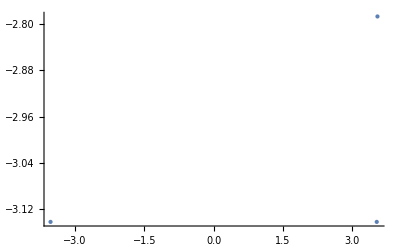

```mathematica
Pl1 = ListPlot[{{Re[Sp1],Im[Sp1]},{Re[Sp2],Im[Sp2]},{Re[3.5409879179647317-2.7867041926350082 ⅈ],Im[3.5409879179647317-2.7867041926350082 ⅈ]}},PlotStyle->PointSize[Large], PlotRange->All,LabelStyle->{12, GrayLevel[0]}] (* Plot the four saddle points with the given parameters and C=-1 *)
```

#### Make contour plots of the exponent to put the saddle points in context:

Contour plot of the real part of the exponent (Pl2) and the imaginary part of the exponent (Pl3), along with the saddle points (Replot and Implot). As before, we are not yet concerned with the complete function since the exponent suffices in allowing us to make the general approximation:

```mathematica
testplot = ContourPlot[Re[ⅈ Scl/.Test/.ϵ->0.2/.{n->nr+ⅈ ni}],{nr, -20, 20},{ ni, -20, 20}, ColorFunction->"TemperatureMap", Contours->100,LabelStyle->{12, GrayLevel[0]}] (* Contour plot of the real part of the exponent. *)
```

-Graphics-

```mathematica
Pl2 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->100,LabelStyle->{12, GrayLevel[0]}] (* Contour plot of the real part of the exponent. *)
```

-Graphics-

```mathematica
Replot=Show[Pl2,Pl1] (* Showing with the saddle points *)
```

-Graphics-

```mathematica
Pl3 = ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}](* Contour plot of the imaginary part of the exponent. *)
```

-Graphics-

```mathematica
Implot=Show[Pl3,Pl1] (* Showing with the saddle points *)
```

-Graphics-

#### Find the lines of steepest descent/ascent:

```mathematica
Sp4
```

-ⅈ (π+2 ArcCos[3])

```mathematica
-ⅈ (π+2 ArcCos[√5])//N
```

2.88727-3.14159 ⅈ

Make a contour plot of the imaginary part of the exponent for the hopefully-relevant saddle point value of the exponent (Pl4). We are looking for lines of steepest descent/ascent, which have constant imaginary parts, so this allows us to see the lines of steepest descent/ascent that pass through the saddle point/s. Note that n is set to Sp4.

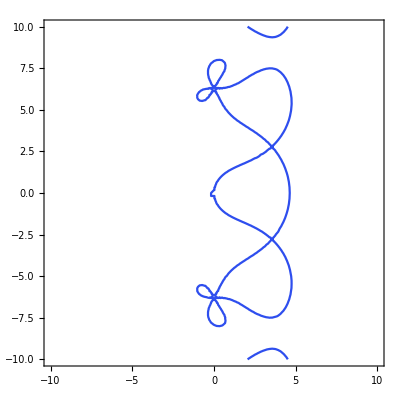

```mathematica
Pl4 = ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl/.Test/.{n->3.5409879179647317-2.7867041926350082 ⅈ}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}] (* Contour plot of imaginary part of exponent evaluated at fourth saddle point *)
```

```mathematica
Lofda=Show[Pl2,Pl1,Pl4] (* Showing altogether the contour for the real part of the exponent (Pl2), the saddle point (Pl1), and the lines of steepest descent/ascent (Pl4) *)
```

-Graphics-

```mathematica
(*Pl5 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Re[ⅈ Scl/ⅇ^0/.Test/.{n->-ⅈ (π+2 ArcCos[√5])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150]*)
```

#### Determine the relevant saddle point/s:

Now, we add a small perturbation to our seemingly endless line of steepest descent/ascent that stems from Sp4 (why?). Explain this step in greater detail. The perturbation is introduced by giving an imaginary component to ℏ (which is set to 1 for now) in the form of ⅇ^ⅈα where α is the perturbation parameter that can be varied to slightly shift the lines of steepest descent/ascent.

```mathematica
Manipulate[
Show[Pl2,Pl1,ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl/ⅇ^(ⅈ α)/.Test/.{n->3.5409879179647317-2.7867041926350082 ⅈ}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}]],
{{α,-0.01},-0.1,0.1}
] (* This is the same plot as Lofda except with a small perturbation. *)
```

Lines of steepest descent and ascent have constant imaginary parts - why?

#### Evaluate (or rather, approximate) the integral:

Plugging in the expression for  for n for the dominant saddle point (with C[1]=-1) into the expression that we are integrating gives us an approximation to the integral.

```mathematica
Cond={C[1]->-1, ta->0,tb->0,xa-> xb-l,m->1,k->1,ℏ->1,ϵ->0.1,H->1}; (* Redefining xa and xb in terms of l=xb-xa *)
Cond1={C[1]->-1, ta->0,tb->0,xa-> xb-l,(*m->1,k->1,*)ℏ->1,ϵ->0.1,H->1};
```

```mathematica
Spfin = FullSimplify[n/.Soln⟦4⟧/.Cond1] (* General expression for n at the dominant saddle point with given parameters *)
```

(2 m (-ⅈ π+ArcSinh[(k √(-l^2))/(2 m)]))/k

```mathematica
FullSimplify[Pref*Exp[ⅈ Scl]]/.Cond1 (* General form of integrand for kernel with given parameters *)
```

(2 ⅇ^(-1/4 ⅈ (2 m n-k l^2 Coth[(k n)/(2 m)])))/(√(-k^2 Csch[(k n)/(2 m)]^2))

```mathematica
g=FullSimplify[Exp[ⅈ Scl/ℏ]/.n->Spfin/.Cond1] (* Most general approximation of the integral using saddle point approx. (disregarding prefactor) *)
```

ⅇ^(-(ⅈ m (k √(-l^2) √(4-(k^2 l^2)/m^2)-4 ⅈ m π+4 m ArcSinh[(k √(-l^2))/(2 m)]))/(4 k))

```mathematica
Simplify[Im[ArcSinh[(k √(-l^2))/(2 m)]]/.{l->2m/k},Assumptions->{m>0,k>0}]
```

π/2

```mathematica
Simplify[Im[ArcSinh[(k √(-l^2))/(2 m)]],Assumptions->{l> 2m/k, l>0,m>0,k>0}]
```

Re[ArcSin[(k l)/(2 m)]]

```mathematica
Simplify[Im[ArcSinh[(k √(-(2m/k+1)^2))/(2 m)]],Assumptions->{l> 2m/k, l>0,m>0,k>0}]
```

Re[ArcSin[1+k/(2 m)]]

```mathematica
Plot[Im[ArcSinh[(k √(-l^2))/(2 m)]/.{m->2,k->1}],{l,0,6}]
```

-Graphics-

For plotting purposes, let' s evaluate g with all parameters defined:

```mathematica
Plot[(Abs[g/.Cond])^2,{l,0,10},PlotRange->All, AxesLabel->{l (Distance), P (Probability)},LabelStyle->{12, GrayLevel[0]}] (* Plot of the probability approximation with respect to l (disregarding prefactor) *)
```

-Graphics-

```mathematica
Lcrit=FullSimplify[Solve[D[(Abs[g])^2, l]==0, l]] (* Determining the critical distance between the particle and antiparticle (before which they remain virtual particles) *)
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

{{l→-(2 m)/k},{l→(2 m)/k}}

```mathematica
IntApprox = FullSimplify[g/.Lcrit⟦2⟧, m ∈Reals && m>0 && k∈ Reals && k>0]  (* Final approximation of kernel with critical distance and other given parameters *)
```

ⅇ^(-(m^2 π)/(2 k))

```mathematica
Prob = IntApprox^2 (* Final approximation of probability with *)
```

ⅇ^(-(m^2 π)/k)

Use n (saddle point) to plot trajectory.

```mathematica
Fcond={l->2m/k,k->1,m->1};
```

```mathematica
Cond1
Fcond
```

```mathematica
{C[1]->-1,ta->0,tb->0,xb->l+xa,ℏ->1}
```

{C[1]→-1,ta→0,tb→0,xb→l+xa,ℏ→1}

```mathematica
nn=FullSimplify[n/.Soln⟦4⟧/.Cond1//.Fcond]
```

-ⅈ π

Lookup de Sitter in Poincare patch (in proper time coordinates and in conformal (time) coordinates)

```mathematica
-dtau^2=ds^2 = -dt^2 + spatial part
= -f(η) dη^2 + spatial part
```

Find derivative of imaginary part of T with respect to internal time, and check which choice of parameters give you negative derivative
ParametricPlot3D for imaginary time, real time, and real x.

```mathematica
Cond2={xa->0,xb->3,ta->0,tb->0,m->1,k->1};
```

```mathematica
ParametricPlot3D[{Re[xm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2],Im[tm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2],Re[tm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-

$Aborted

-k (-(k n (Cosh[(k n T)/m]-Sinh[(k n T)/m]) (1))/(16 m^2 (-1+Cosh[(k n)/m]+Sinh[(k n)/m])^3)+((Cosh[(k n T)/m]-Sinh[(k n T)/m]) (1))/(16 m (-1+Cosh[(k n)/m]+Sinh[(k n)/m])^3))+(m ((k^2 n^2 1 (1))/(16 m^3 1^3)-1+1/1))/n+(ϵ (H m (1) (-(k n 1 ((1) (1)+18))/(16 m^2 (1)^3)+((1) 1)/(16 m 1^3))+1/1))/n
 |  |  |  |

1) Try saddle point (n1) with a few values of ϵ -> shifts should be linear
2) Saddle points as function of ϵ (analytic background + perturbation) -> 
3) Literature -> try and find out kinds of electric field -> even if flat minkowski, diff kinds of electric field -> Dunne et al.

```mathematica
ParametricPlot[{Re[solx/.Test/.Solnn3//.ϵ->0.4],Im[solt/.Test/.Solnn3//.ϵ->0.4]},{T,0,1},AspectRatio->1]
```

```mathematica
ParametricPlot3D[{Re[solx//.Test//.Solnn//.ϵ->0.1],Im[solt//.Test//.Solnn//.ϵ->0.1],Re[solt//.Test//.Solnn//.ϵ->0.1]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Re[solx//.Test//.Solnn1//.ϵ->0.2],Im[solt//.Test//.Solnn1//.ϵ->0.2],Re[solt//.Test//.Solnn1//.ϵ->0.2]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Re[solx//.Test//.Solnn2//.ϵ->0.3],Im[solt//.Test//.Solnn2//.ϵ->0.3],Re[solt//.Test//.Solnn2//.ϵ->0.3]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Re[solx//.Test//.Solnn3//.ϵ->0.4],Im[solt//.Test//.Solnn3//.ϵ->0.4],Re[solt//.Test//.Solnn3//.ϵ->0.4]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Re[solx//.Test//.Solnn4//.ϵ->0.5],Im[solt//.Test//.Solnn4//.ϵ->0.5],Re[solt//.Test//.Solnn4//.ϵ->0.5]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Re[solx//.Test//.Solnn5//.ϵ->0.6],Im[solt//.Test//.Solnn5//.ϵ->0.6],Re[solt//.Test//.Solnn5//.ϵ->0.6]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Re[solx//.Test//.Solnn6//.ϵ->0.7],Im[solt//.Test//.Solnn6//.ϵ->0.7],Re[solt//.Test//.Solnn6//.ϵ->0.7]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-